```mathematica
ClearAll["Global`*"];
(*Define the system of equations*)
u[k_,t_]:=Apply[Plus,Table[m[j][t]((x[j][t]-x[k][t])Sign[x[j][t]-x[k][t]]),{j,1,n}]]
ux[k_,t_]:=Apply[Plus,Table[-m[j][t]Sign[x[j][t]-x[k][t]],{j,1,n}]]

(*Define the number of equations*)
n=2; (*Example for n=5*)

(*Define initial conditions*)
initialConditions=Flatten[Table[{m[i][0]==RandomReal[{1,10}],x[i][0]==RandomReal[{1,10}]},{i,n}]];
initialConditions={
m[1][0]==1,x[1][0]==0,
m[2][0]==2,x[2][0]==1
};

(*Define the system of ODEs*)
eqns=Flatten[Table[{
m[i]'[t]==-m[i][t]ux[i,t]u[i,t],
x[i]'[t]==u[i,t]^2},
{i,n}
]];

(*Solve the system numerically*)
Tstart=-Pi/4;
Tend=Pi/2;
T={t,Tstart,Tend};
threshold=10^5;  (*Threshold for wrap-around*)
wrapEvents={
WhenEvent[x[2][t]>threshold,x[2][t]->-threshold+5],
WhenEvent[x[1][t]>threshold,x[1][t]->-threshold+5],
WhenEvent[x[2][t]<-threshold,x[2][t]->threshold-5],
WhenEvent[x[1][t]<-threshold,x[1][t]->threshold-5]
};
sol=NDSolve[Join[eqns,initialConditions,wrapEvents],Flatten[Table[{m[i],x[i]},{i,n}]],T];

M1=2;
M2=1;

ParametricPlot[Evaluate[Table[{x[i][t],m[i][t]}/. sol,{i,n}]],T,PlotRange->All]
```

Which[MatchQ[{_,_,_}],System`SampledPlotsDump`iParametricPlot[ParametricPlot,{{{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}},{{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}}},Evaluate[T],Evaluate[],PlotRange→All],!MatchQ[Evaluate[T],{_,_,_}],Message[ParametricPlot::pllim,T];Throw[$Failed,ChartingError],!MatchQ[Evaluate[],{_,_,_}],Message[ParametricPlot::pllim,HoldForm[]];Throw[$Failed,ChartingError]]

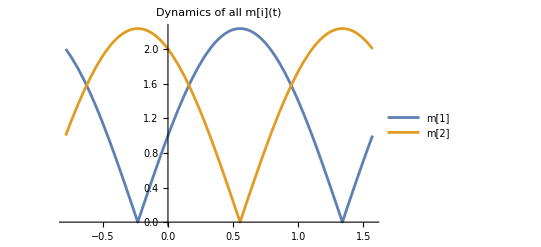

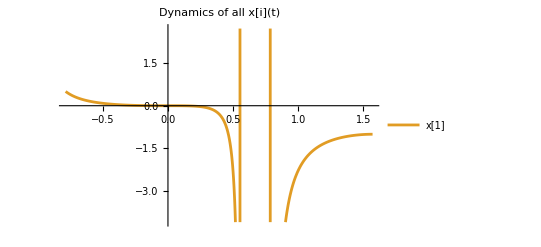

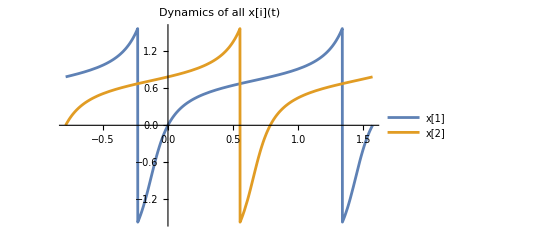

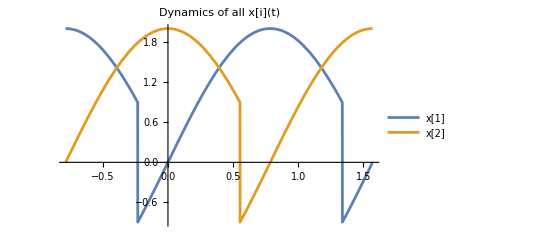

```mathematica
(*Plot all m[i]'s together*)plotM=Plot[Evaluate[Table[m[i][t]/. sol,{i,n}]],T,PlotLegends->Table["m["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all m[i](t)",PlotStyle->Array[ColorData[97],n]]

(*Plot all x[i]'s together*)
plotX=Plot[Evaluate[Table[((M2/M1)Tan[M2 t+Pi/4]-x[i][t]+0.5)/. sol,{i,2,2}]],T,PlotLegends->Table["x["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all x[i](t)",PlotStyle->Array[ColorData[97],n]]

(*Plot all x[i]'s together*)
plotX=Plot[Evaluate[Table[ArcTan[x[i][t]]/. sol,{i,n}]],T,PlotLegends->Table["x["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all x[i](t)",PlotStyle->Array[ColorData[97],n]]

(*Plot all x[i]'s together*)
plotX=Plot[Evaluate[Table[x[i][t]m[i][t]/. sol,{i,n}]],T,PlotLegends->Table["x["<>ToString[i]<>"]",{i,n}],PlotLabel->"Dynamics of all x[i](t)",PlotStyle->Array[ColorData[97],n]]


(*Display the plots*)
GraphicsColumn[{plotM,plotX}];
x[1][Tend]/.sol[[1]];
x[2][Tstart]/.sol[[1]];
```

```mathematica
M1=(m[1][0]m[2][0](x[2][0]-x[1][0])+m[1][0]m[3][0](x[3][0]-x[1][0])+m[2][0]m[3][0](x[3][0]-x[2][0]))/.sol[[1]]
M2=(m[1][0]m[2][0]m[3][0])^2(x[2][0]-x[1][0])(x[3][0]-x[1][0])(x[3][0]-x[2][0])/.sol[[1]]
A1=m[1][0]^2(M1+2m[2][0]m[3][0](x[3][0]-x[2][0]));
A2=m[2][0]^2(M1+2m[1][0]m[3][0](x[3][0]-x[1][0]));
A3=m[3][0]^2(M1+2m[1][0]m[2][0](x[2][0]-x[1][0]));
M3=(A1 x[1][0]^0+A2 x[2][0]^0+A3 x[2][0]^0)/.sol[[1]]
M3=(A1 x[1][0]^1+A2 x[2][0]^1+A3 x[2][0]^1)/.sol[[1]]
M3=(A1 x[1][0]^2+A2 x[2][0]^2+A3 x[2][0]^2)/.sol[[1]]
```

Part::partd: Part specification sol⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {sol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

m[1][0] m[2][0] (-x[1][0]+x[2][0])+m[1][0] m[3][0] (-x[1][0]+x[3][0])+m[2][0] m[3][0] (-x[2][0]+x[3][0])/.sol⟦1⟧

Part::partd: Part specification sol⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {sol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(m[1][0])^2 (m[2][0])^2 (m[3][0])^2 (-x[1][0]+x[2][0]) (-x[1][0]+x[3][0]) (-x[2][0]+x[3][0])/.sol⟦1⟧

Part::partd: Part specification sol⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {sol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(m[3][0])^2 ((m[1][0] m[2][0] (-x[1][0]+x[2][0])+m[1][0] m[3][0] (-x[1][0]+x[3][0])+m[2][0] m[3][0] (-x[2][0]+x[3][0])/.sol⟦1⟧)+2 m[1][0] m[2][0] (-x[1][0]+x[2][0]))+(m[2][0])^2 ((m[1][0] m[2][0] (-x[1][0]+x[2][0])+m[1][0] m[3][0] (-x[1][0]+x[3][0])+m[2][0] m[3][0] (-x[2][0]+x[3][0])/.sol⟦1⟧)+2 m[1][0] m[3][0] (-x[1][0]+x[3][0]))+(m[1][0])^2 ((m[1][0] m[2][0] (-x[1][0]+x[2][0])+m[1][0] m[3][0] (-x[1][0]+x[3][0])+m[2][0] m[3][0] (-x[2][0]+x[3][0])/.sol⟦1⟧)+2 m[2][0] m[3][0] (-x[2][0]+x[3][0]))/.sol⟦1⟧

Part::partd: Part specification sol⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {sol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(m[3][0])^2 x[2][0] ((m[1][0] m[2][0] (-x[1][0]+x[2][0])+m[1][0] m[3][0] (-x[1][0]+x[3][0])+m[2][0] m[3][0] (-x[2][0]+x[3][0])/.sol⟦1⟧)+2 m[1][0] m[2][0] (-x[1][0]+x[2][0]))+(m[2][0])^2 x[2][0] ((m[1][0] m[2][0] (-x[1][0]+x[2][0])+m[1][0] m[3][0] (-x[1][0]+x[3][0])+m[2][0] m[3][0] (-x[2][0]+x[3][0])/.sol⟦1⟧)+2 m[1][0] m[3][0] (-x[1][0]+x[3][0]))+(m[1][0])^2 x[1][0] ((m[1][0] m[2][0] (-x[1][0]+x[2][0])+m[1][0] m[3][0] (-x[1][0]+x[3][0])+m[2][0] m[3][0] (-x[2][0]+x[3][0])/.sol⟦1⟧)+2 m[2][0] m[3][0] (-x[2][0]+x[3][0]))/.sol⟦1⟧

Part::partd: Part specification sol⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {sol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(m[3][0])^2 (x[2][0])^2 ((m[1][0] m[2][0] (-x[1][0]+x[2][0])+m[1][0] m[3][0] (-x[1][0]+x[3][0])+m[2][0] m[3][0] (-x[2][0]+x[3][0])/.sol⟦1⟧)+2 m[1][0] m[2][0] (-x[1][0]+x[2][0]))+(m[2][0])^2 (x[2][0])^2 ((m[1][0] m[2][0] (-x[1][0]+x[2][0])+m[1][0] m[3][0] (-x[1][0]+x[3][0])+m[2][0] m[3][0] (-x[2][0]+x[3][0])/.sol⟦1⟧)+2 m[1][0] m[3][0] (-x[1][0]+x[3][0]))+(m[1][0])^2 (x[1][0])^2 ((m[1][0] m[2][0] (-x[1][0]+x[2][0])+m[1][0] m[3][0] (-x[1][0]+x[3][0])+m[2][0] m[3][0] (-x[2][0]+x[3][0])/.sol⟦1⟧)+2 m[2][0] m[3][0] (-x[2][0]+x[3][0]))/.sol⟦1⟧